Evolution of sex roles: Mathematical analysis

Figure 2a

```mathematica
(*  Parameters:
d: care demand of offspring, d = 20
u: mortality rate for both males and females, u =0.001
 TM: male care, allow to evolve
    TF: female care, allow to evolve

Offspring survival function:
S = (TM + TF)^2 / ((TM + TF)^2 + d^2)  *)
```

```mathematica
(*Selection gradient for male care*)

sgMale[TM_,TF_]:=(2 * d^2 *ⅇ^(-TM u))/(((((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))^2 + d^2)*(((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))) +(((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2)+u) *(-u)*ⅇ^(-TM u))/(1- ((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2)+u) *  ⅇ^(-TM u))

(*Selection gradient for female care*)

sgFemale[TM_,TF_]:=(2 *d^2 *ⅇ^(-TF u))/(((((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))^2 + d^2)*(((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u )))  +(((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2)+u) *(-u)*ⅇ^(-TF u))/(1- ((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2)+u) *  ⅇ^(-TF u))
```

{d→20,u→0.001}

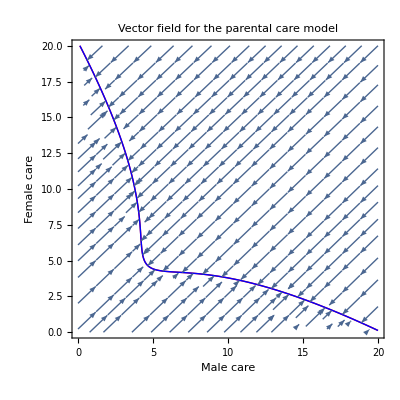

```mathematica
(*Coevolution of male care and female care*)
pars={d->20,u->0.001}

plot1=ContourPlot[sgMale[TM,TF]/.pars,{TM,0,20},{TF,0,20},Contours->{0},ContourShading->None,ContourStyle->Red,MaxRecursion->10];
plot2=ContourPlot[sgFemale[TM,TF]/.pars,{TM,0,20},{TF,0,20},Contours->{0},ContourShading->None,ContourStyle->Blue,MaxRecursion->10];
plot3=StreamPlot[{sgMale[TM,TF],sgFemale[TM,TF]}/.pars,{TM,0,20},{TF,0,20}];
Show[{plot1,plot2,plot3}, PlotLabel-> "Vector field for the parental care model", FrameLabel-> {"Male care",  "Female care"}]
```

Supplementary Figure S8a

```mathematica
(*    Parameters:
a: the parameter of offspring survival function in Fromhage and Jennions (2016); a = 0.1 or a = 20
u: mortality rate for both males and females; u = 0.01 or u = 0.001
  TM: male care, allow to evolve
       TF: female care, allow to evolve

Offspring survival function:
   S = exp (-a /(TM + TF))      *)
```

```mathematica
(*Selection gradient for male care*)
SGmale[TM_,TF_]:=(a *ⅇ^(-TM u))/((((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))^2)  +(((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2)+u) *(-u)*ⅇ^(-TM u))/(1- ((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2)+u) *  ⅇ^(-TM u))

(*Selection gradient for female care*)
SGfemale[TM_,TF_]:=(a *ⅇ^(-TF u))/((((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))^2) +(((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2)+u) *(-u)*ⅇ^(-TF u))/(1- ((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2)+u) *  ⅇ^(-TF u))
```

{a→0.1,u→0.01}

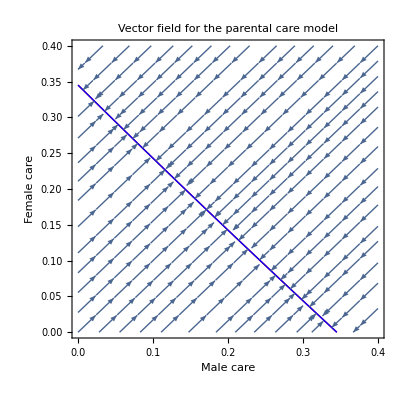

```mathematica
(*Supplementary Figure S5a: Figure 1a in Fromhage and Jennions (2016)*)
pars={a->0.1,u->0.01}

plot1=ContourPlot[SGmale[TM,TF]/.pars,{TM,0,0.4},{TF,0,0.4},Contours->{0},ContourShading->None,ContourStyle->Red,MaxRecursion->10];
plot2=ContourPlot[SGfemale[TM,TF]/.pars,{TM,0,0.4},{TF,0,0.4},Contours->{0},ContourShading->None,ContourStyle->Blue,MaxRecursion->10];
plot3=StreamPlot[{SGmale[TM,TF],SGfemale[TM,TF]}/.pars,{TM,0,0.4},{TF,0,0.4}];
Show[{plot1,plot2,plot3}, PlotLabel-> "Vector field for the parental care model", FrameLabel-> {"Male care",  "Female care"}]
```

{a→20,u→0.001}

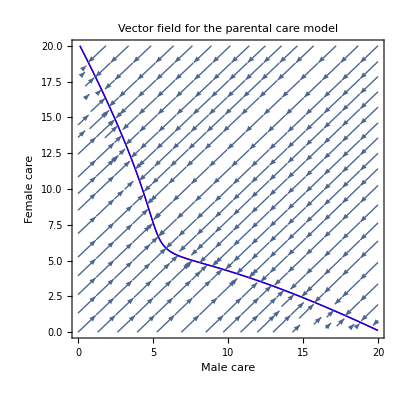

```mathematica
(*Supplementary Figure S5b: rescaled version of Fromhage and Jennions (2016)*)
pars={a->20,u->0.001}

plot1=ContourPlot[SGmale[TM,TF]/.pars,{TM,0,20},{TF,0,20},Contours->{0},ContourShading->None,ContourStyle->Red,MaxRecursion->10];
plot2=ContourPlot[SGfemale[TM,TF]/.pars,{TM,0,20},{TF,0,20},Contours->{0},ContourShading->None,ContourStyle->Blue,MaxRecursion->10];
plot3=StreamPlot[{SGmale[TM,TF],SGfemale[TM,TF]}/.pars,{TM,0,20},{TF,0,20}];
Show[{plot1,plot2,plot3}, PlotLabel-> "Vector field for the parental care model", FrameLabel-> {"Male care",  "Female care"}]
```

Supplementary Figure S2

```mathematica
(*    Parameters:
d: care demand of offspring, d = 20
u: mortality rate for both males and females, u =0.001
   T: parental care of the resident population
   Tmut: parental care of rare mutants

Offspring survival of the mutant in the resident population:
S = (T + Tmut)^2 / ((T + Tmut)^2 + d^2)        *)
```

```mathematica
(*Fitness of resident population*)

fitRes1 = ((T + T)^2 / ((T + T)^2 + d^2)) * (1/(1+u -ⅇ^(-T * u)))

(*Fitness of a mutant in the resident population*)

fitMut1= ((T + Tmut)^2 / ((T + Tmut)^2 + d^2)) * (1/(1+u -ⅇ^(-Tmut * u)))

(*Selection gradient*)

grad1= D[fitMut1, Tmut]/.{Tmut->T} // FullSimplify

(*Evolutionarily singular strategy*)

FindRoot[grad1==0 /.{u->  0.001,d-> 20},{T,0.0001,20}]
(*T == 4.665565694341089*)
```

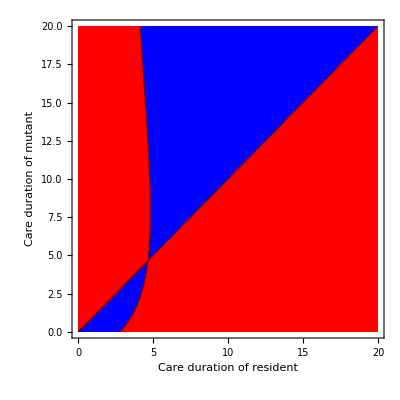

```mathematica
(*Pairwise invasibility plot*)
deltaW1 = fitMut1-fitRes1(*The mutant has a higher fitness than the resident can invade the resident population*)
p1 = ContourPlot[deltaW1/. {u->  0.001, r -> 0,d-> 20},{T,0.0,20.0},{Tmut,0.0,20.0},Contours->{0},PlotPoints->100,PlotRange->All,ContourShading->{Blue,Red},
LabelStyle->Directive[FontFamily->"Arial",FontSize->20],FrameLabel-> {"Care duration of resident",  "Care duration of mutant"}]
```

Supplementary Figure S10

```mathematica
(*    Parameters:
a: parameter in offspring survival function, a = 20
u: mortality rate for both males and females, u =0.001
   T: parental care of the resident population
   Tmut: parental care of rare mutants

Offspring survival of the mutant in the resident population:
S = exp (-a/(T + Tmut))      *)
```

```mathematica
(*Fitness of resident population*)

fitRes2 = ⅇ^(-a/(T+T)) * (1/(1+u -ⅇ^(-T * u)))

(*Fitness of a mutant in the resident population*)

fitMut2 = ⅇ^(-a/(T+Tmut)) * (1/(1+u -ⅇ^(-Tmut * u)))
(*Selection gradient*)

grad2= D[fitMut2, Tmut]/.{Tmut->T} // FullSimplify

(*Evolutionarily singular strategy*)

FindRoot[grad2==0 /.{u->  0.001,a-> 20},{T,1,20}]
(*T == 5.871319152843298*)
```

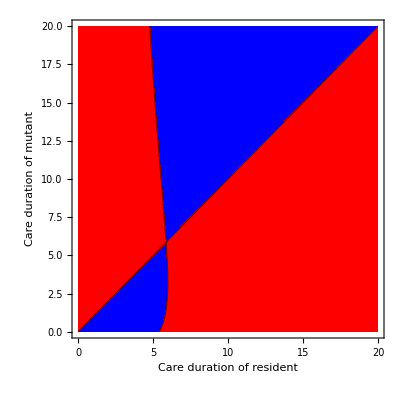

```mathematica
(*Pairwise invasibility plot*)
deltaW2 = fitMut2-fitRes2 (*The mutant has a higher fitness than the resident can invade the resident population*)
p2 = ContourPlot[deltaW2 /. {u->  0.001,a-> 20},{T,0.0,20.0},{Tmut,0.0,20.0},Contours->{0},PlotPoints->100,PlotRange->All,ContourShading->{Blue,Red},
LabelStyle->Directive[FontFamily->"Arial",FontSize->20],FrameLabel-> {"Care duration of resident",  "Care duration of mutant"}]
```